This is for x*sin(2*x)*exp(-10 * x**2)

```mathematica
x = {-1.,-0.97979798,-0.95959596,-0.93939394,-0.91919192,-0.8989899,-0.87878788,-0.85858586,-0.83838384,-0.81818182,-0.7979798,-0.77777778,-0.75757576,-0.73737374,-0.71717172,-0.6969697,-0.67676768,-0.65656566,-0.63636364,-0.61616162,-0.5959596,-0.57575758,-0.55555556,-0.53535354,-0.51515152,-0.49494949,-0.47474747,-0.45454545,-0.43434343,-0.41414141,-0.39393939,-0.37373737,-0.35353535,-0.33333333,-0.31313131,-0.29292929,-0.27272727,-0.25252525,-0.23232323,-0.21212121,-0.19191919,-0.17171717,-0.15151515,-0.13131313,-0.11111111,-0.09090909,-0.07070707,-0.05050505,-0.03030303,-0.01010101,0.01010101,0.03030303,0.05050505,0.07070707,0.09090909,0.11111111,0.13131313,0.15151515,0.17171717,0.19191919,0.21212121,0.23232323,0.25252525,0.27272727,0.29292929,0.31313131,0.33333333,0.35353535,0.37373737,0.39393939,0.41414141,0.43434343,0.45454545,0.47474747,0.49494949,0.51515152,0.53535354,0.55555556,0.57575758,0.5959596,0.61616162,0.63636364,0.65656566,0.67676768,0.6969697,0.71717172,0.73737374,0.75757576,0.77777778,0.7979798,0.81818182,0.83838384,0.85858586,0.87878788,0.8989899,0.91919192,0.93939394,0.95959596,0.97979798,1.};
y= {-4.12820393*10^-05,-6.26712281*10^-05,-9.41894090*10^-05,-1.40148426*10^-04,-2.06465966*10^-04,-3.01162781*10^-04,-4.34972819*10^-04,-6.22076104*10^-04,-8.80958438*10^-04,-1.23539323*10^-03,-1.71552828*10^-03,-2.35904392*10^-03,-3.21232837*10^-03,-4.33159222*10^-03,-5.78381691*10^-03,-7.64740437*10^-03,-1.00123686*10^-02,-1.29798880*10^-02,-1.66610243*10^-02,-2.11744131*10^-02,-2.66427491*10^-02,-3.31879258*10^-02,-4.09247554*10^-02,-4.99532813*10^-02,-6.03498108*10^-02,-7.21569322*10^-02,-8.53729279*10^-02,-9.99411481*10^-02,-1.15740053*10^-01,-1.32574741*10^-01,-1.50170859*10^-01,-1.68171795*10^-01,-1.86139980*10^-01,-2.03563003*10^-01,-2.19864981*10^-01,-2.34423325*10^-01,-2.46590675*10^-01,-2.55721331*10^-01,-2.61201124*10^-01,-2.62479235*10^-01,-2.59100178*10^-01,-2.50733934*10^-01,-2.37202147*10^-01,-2.18498382*10^-01,-1.94800712*10^-01,-1.66475280*10^-01,-1.34070079*10^-01,-9.82988015*10^-02,-6.00153225*10^-02,-2.01800458*10^-02,2.01800458*10^-02,6.00153225*10^-02,9.82988015*10^-02,1.34070079*10^-01,1.66475280*10^-01,1.94800712*10^-01,2.18498382*10^-01,2.37202147*10^-01,2.50733934*10^-01,2.59100178*10^-01,2.62479235*10^-01,2.61201124*10^-01,2.55721331*10^-01,2.46590675*10^-01,2.34423325*10^-01,2.19864981*10^-01,2.03563003*10^-01,1.86139980*10^-01,1.68171795*10^-01,1.50170859*10^-01,1.32574741*10^-01,1.15740053*10^-01,9.99411481*10^-02,8.53729279*10^-02,7.21569322*10^-02,6.03498108*10^-02,4.99532813*10^-02,4.09247554*10^-02,3.31879258*10^-02,2.66427491*10^-02,2.11744131*10^-02,1.66610243*10^-02,1.29798880*10^-02,1.00123686*10^-02,7.64740437*10^-03,5.78381691*10^-03,4.33159222*10^-03,3.21232837*10^-03,2.35904392*10^-03,1.71552828*10^-03,1.23539323*10^-03,8.80958438*10^-04,6.22076104*10^-04,4.34972819*10^-04,3.01162781*10^-04,2.06465966*10^-04,1.40148426*10^-04,9.41894090*10^-05,6.26712281*10^-05,4.12820393*10^-05};
```

```mathematica
data =Transpose[{x,y}];
```

```mathematica
form = FindFormula[data]
```

1.99963 #1-21.2971 #1^3.+112.559 #1^5.-388.688 #1^7.+962.29 #1^9.-1753.55 #1^11.+2332.19 #1^13.-2193.84 #1^15.-923.95 #1^17.+2304.17 Cos[#1] #1^17.+627.338 #1^19.&

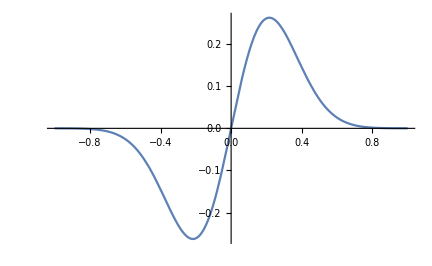

```mathematica
Plot[form[x],{x,-1,1}]
```

```mathematica
form[z]
```

1.99963 z-21.2971 z^3.+112.559 z^5.-388.688 z^7.+962.29 z^9.-1753.55 z^11.+2332.19 z^13.-2193.84 z^15.-923.95 z^17.+627.338 z^19.+2304.17 z^17. Cos[z]